## Random Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=RandomInteger[9,10000];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.19652,0.948185}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

{0.19652,0.948185,4.918}

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,8→442,3→2180,7→654,4→1586,5→1170,6→841,2→1925,9→382,12→127,10→223,11→186,13→94,16→38,14→64,15→41,19→7,23→2,17→19,18→9,27→1,21→3,20→4,22→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

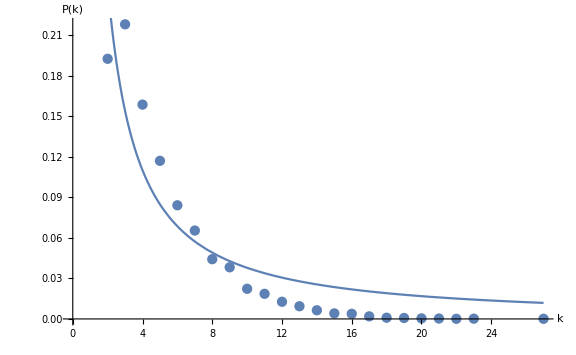
{{{0.553805,0.193716},{1.1658,0.273332}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{0.19652,0.948185,4.918,{{0.553805,0.193716},{1.1658,0.273332}}}

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

{0.19652,0.948185,4.918,{{0.553805,0.193716},{1.1658,0.273332}},3.4138}

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,4→1597,3→2365,6→586,2→3858,5→1037,7→318,8→158,9→56,10→22,12→1,11→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

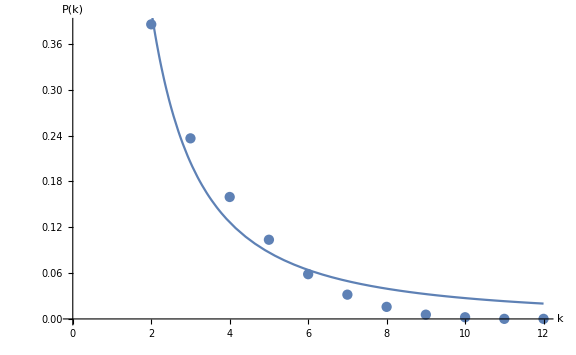
{{{1.2909,0.418154},{1.67527,0.335524}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{0.19652,0.948185,4.918,{{0.553805,0.193716},{1.1658,0.273332}},3.4138,{{1.2909,0.418154},{1.67527,0.335524}}}